```mathematica
sol1 = DSolve[{2y''[x]+3y'[x]+5y[x]==11e^(-x),y[0]==7,y'[0]==13},y[x],x] //FullSimplify
```

{{y[x]→(e^-x ⅇ^(-3 x/4) (341 ⅇ^(3 x/4)+e^x (31 Cos[(√31 x)/4] (24+7 Log[e] (-3+2 Log[e]))+√31 (332+Log[e] (-175+146 Log[e])) Sin[(√31 x)/4])))/(31 (5+Log[e] (-3+2 Log[e])))}}

```mathematica
Plot[Evaluate[y[x]/.sol],{x,-1000000000,1000000000}]
```

```mathematica
sol=DSolve[{y''[x]/y[x]==-4*Exp[-x/4],y[0]==15,y'[0]==1/2},y,x]
```

{{y→Function[{x},(BesselJ[0,16 √(ⅇ^(-x/4))] BesselY[0,16]-BesselJ[0,16] BesselY[0,16 √(ⅇ^(-x/4))]+60 BesselJ[1,16] BesselY[0,16 √(ⅇ^(-x/4))]-60 BesselJ[0,16 √(ⅇ^(-x/4))] BesselY[1,16])/(4 (BesselJ[1,16] BesselY[0,16]-BesselJ[0,16] BesselY[1,16]))]}}

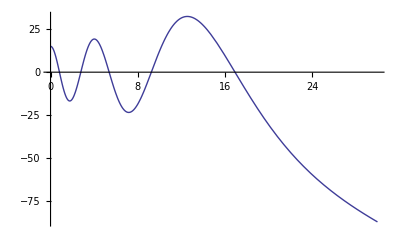

```mathematica
Plot[Evaluate[y[x]/.sol],{x,0,30}]
```

```mathematica
aSol =DSolve[{5 y[x]+3 y'[x]+2 y''[x]==11 Exp[-x],y'[0]==13,y[0]==7},y[x],x]
```

{{y[x]→1/124 ⅇ^-x (527 ⅇ^(x/4) Cos[(√31 x)/4]+341 Cos[(√31 x)/4]^2+303 √31 ⅇ^(x/4) Sin[(√31 x)/4]+341 Sin[(√31 x)/4]^2)}}

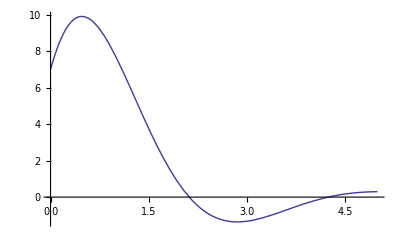

```mathematica
Plot[Evaluate[y[x]/.aSol],{x,0,5}]
```

```mathematica
3
```

```mathematica
aSol =DSolve[{5 y[x]+3 y'[x]+2 y''[x]==11 Exp[-x],y'[0]==13,y[0]==7},y[x],x]
```

```mathematica
rk4 = Import["/home/dk0r/git/comp-phys/HW_3/test.csv"]
```

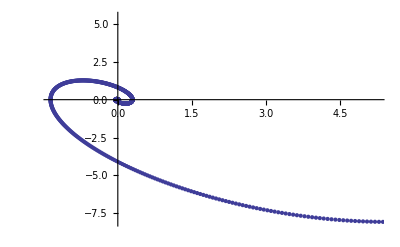

```mathematica
ListPlot[{rk4}]
```

```mathematica
ij.combined = Import["/home/dk0r/git/comp-phys/HW_3/ij.combined.csv"]
```